{53.6744,41.8355,26.5992,9.32135,6.36063}

{-52.5108,-52.0099,-51.5227,-51.0389,-50.4419}

{0.46156,0.37946,0.139824,0.0119021,0.00725262}

0.851474

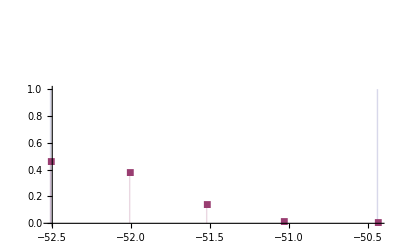

```mathematica
n=5;
(*H0=-IdentityMatrix[n];*)
H0=1/2 Table[If[i==j,1/1(-(n-i+1))+1/4(RandomReal[]-0.5)-100,0],{i,1,n},{j,1,n}];
(*h={0.,3.2,4.58,4.91,5.80,6.51,6.94,7.65,8.78,10.55,13.3};
n=Length[h];
H0=Table[If[i==j,h[[i]]-0 7.36*22-  13.26,0],{i,1,n},{j,1,n}];
*)
V=Table[If[i<j,(-RandomReal[] 100)/((h[[i]]+1)Abs[H0[[i,i]]-H0[[j,j]]])If[h[[i]]<7 && h[[j]]>7,0.,1],0.],{i,1,n},{j,1,n}];
MatrixForm[V];
V=V+Transpose[V];
H=H0+V;
H//MatrixForm;
V1=Table[Abs[Mean[DeleteCases[V[[i]],0]]],{i,1,n}]
E0=Table[H[[i,i]],{i,1,n}]
Eg=Eigensystem[H0+V];
E1=Eg[[1]];
β1=Eg[[2,1;;-1,1]]^2 ;(* SF of ground state for each state *)
β2=Eg[[2,1]]^2 (* SF of each origin state *)
dEavg=Total[Total[Table[If[i>j,H[[i,i]]-H[[j,j]],0],{i,1,n},{j,1,n}]]]/((n-1)(n-2))
ListPlot[
{
Table[{E0[[i]],V1[[i]]},{i,1,n}]
,Table[{E0[[i]],β2[[i]]},{i,1,n}]
(*,Table[{E1[[i]],β1[[i]]},{i,1,n}]*)
}
,Filling->Axis,PlotRange->{All,{0,1}},PlotMarkers->Automatic]
```

```mathematica
Eg[[2]]//MatrixForm
```

(-0.679382 | -0.616004 | -0.373931 | -0.109097 | -0.0851623
0.717284 | -0.635529 | -0.270193 | 0.0818343 | -0.0436375
-0.149955 | -0.219205 | 0.302146 | 0.823226 | 0.400585
0.036478 | -0.00311843 | -0.157876 | -0.379485 | 0.910893
-0.0111942 | -0.410587 | 0.819118 | -0.399613 | -0.0254695)

```mathematica
v=Eg[[2]][[1]]
(H0+V).v
```

{-0.679382,-0.616004,-0.373931,-0.109097,-0.0851623}

{169.72,153.887,93.4135,27.254,21.2748}